```mathematica
data=Import["D:\\Projects\\VisualStudio\\SEIRSSIM\\SEIRSSIM\\curve.txt"];
```

```mathematica
raw=StringSplit[data];
```

```mathematica
St=Table[ToExpression[raw[[5*i+2]]],{i,0,999}];
Et=Table[ToExpression[raw[[5*i+3]]],{i,0,999}];
It=Table[ToExpression[raw[[5*i+4]]],{i,0,999}];
Rt=Table[ToExpression[raw[[5*i+5]]],{i,0,999}];
```

```mathematica
Et[[1]]
```

1000

```mathematica
Et[[2]]
```

1136

```mathematica
raw[[7]]
```

7413

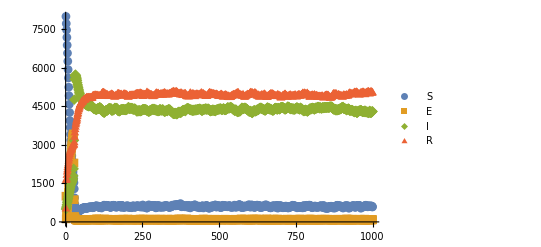

```mathematica
ListPlot[{St,Et,It,Rt},PlotRange->Full,PlotLegends->{"S","E","I","R"},PlotMarkers->Automatic]
```

```mathematica
S[[2]]
Values
```

1+7413

```mathematica
ListPlot[%]
```

-Graphics-